# 1:A Building Equations and Matrices

Numerical Linear Algebra underlies almost every technical computation.  It is how equations are encoded and solved.

## Fitting Data with Polynomials

Suppose I have a bunch of points from a function and I want to run a polynomial p through the points!

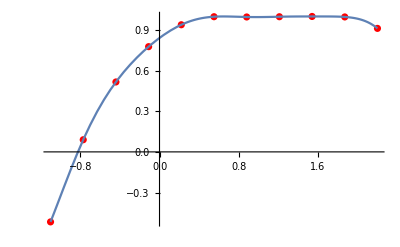

```mathematica
f[x_]:=Sin[x+ Cos[x Sin[x]]]
{a,b}={-1.1,2.2};m=11;
xs=Table[x,{x,a,b,(b-a)/(m-1)}];
fs=Map[f,xs];
Data=Transpose[{xs,fs}];
Show[ListPlot[Data,PlotStyle->Red],Plot[f[x],{x,a,b}]]
```

The polynomial is simply a sum p[x]=a_0+a_1 x+a_2 x^2+… We have m points we should be able to choose m constants to go through the m points. The m equations are 
	a_0 | + | a_1 x_1 | + | a_1 x_1^1 | + | a_2 x_1^2 | + | … | + | a_(m-1)x_1^(m-1) | = | f(x_1)
a_0 | + | a_1 x_2 | + | a_1 x_2^1 | + | a_2 x_2^2 | + | … | + | a_(m-1)x_2^(m-1) | = | f(x_2)
  |   |   |   |   |   |   |   |   |   |   | ⋮ |  
a_0 | + | a_1 x_m | + | a_1 x_m^1 | + | a_2 x_m^2 | + | … | + | a_(m-1)x_m^(m-1) | = | f(x_m)

0.841896+0.542329 x-0.440906 x^2-0.107861 x^3-0.102356 x^4+0.45399 x^5-0.0522185 x^6-0.236959 x^7+0.0902308 x^8+0.0143438 x^9-0.00777293 x^10

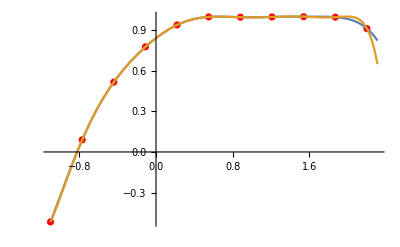

```mathematica
Clear[p]
A=Table[x^(j-1),{x,xs},{j,m}]; 
MatrixForm[A];
as=LinearSolve[A,fs];
p[x_]=Sum[as[[j]] x^(j-1),{j,1,m}]
Show[ListPlot[Data,PlotStyle->Red],Plot[{f[x],p[x]},{x,a,b+0.11}],
PlotRange->All]
```

## Radial Basis Function Interpolation:

A radial basis function is of the form
	ϕ(||x-x_0||)
for some shape functionϕ:ℝ→ℝ. A radial basis function interpolant for a set of m points 
	{x_1,f_1},{x_2,f_2},…,{x_m,f_m}
with the shape function ϕ is simply
	g(x)=∑_(i=1)^m c_i ϕ(||x-x_i||)
where the vector of constants c is chosen to satisfy
	g(x_1)=f_1,g(x_2)=f_2,…,g(x_m)=f_m.
We want to compute this interpolant.

Note that if we want g(x_1)=f_1 then we need 
	ϕ(r_11)c_1 | + | ϕ(r_12)c_2 | + | ϕ(r_13)c_3 | + | … | + | ϕ(r_(1m))c_m | = | f_1 
where r_ij=||x_i-x_j||.
Similarly if we want g(x_2)=f_2 then we need 
	ϕ(r_21)c_1 | + | ϕ(r_22)c_2 | + | ϕ(r_23)c_3 | + | … | + | ϕ(r_(2m))c_m | = | f_2.
There is nothing special about i=1 or i=2. The linear equation for g(x_i)=f_i is
	 ϕ(r_i1)c_1 | + | ϕ(r_i2)c_2 | + | ϕ(r_i3)c_3 | + | … | + | ϕ(r_im)c_m | = | f_i.
The last linear equation is given by i=m. Writing down the whole block of linear equations we get
	ϕ(r_11)c_1 | + | ϕ(r_12)c_2 | + | ϕ(r_13)c_3 | + | … | + | ϕ(r_(1m))c_m | = | f_1
ϕ(r_21)c_1 | + | ϕ(r_22)c_2 | + | ϕ(r_23)c_3 | + | … | + | ϕ(r_(2m))c_m | = | f_2
  | ⋮ |   |   |   |   |   |   |   | ⋮ |  
ϕ(r_i1)c_1 | + | ϕ(r_i2)c_2 | + | ϕ(r_i3)c_3 | + | … | + | ϕ(r_im)c_m | = | f_i
  | ⋮ |   |   |   |   |   |   |   | ⋮ |  
ϕ(r_m1)c_1 | + | ϕ(r_m2)c_2 | + | ϕ(r_m3)c_3 | + | … | + | ϕ(r_mm)c_m | = | f_m
This is of course the reason matrices were invented and this is 
	A.c=f
where the m×m matrix A has entries A_ij=ϕ(||x_i-x_j||).  Any such interpolation matrix is obviously symmetric e.e. A_ij=A_ji.

Lets implement this and see how well it works with x∈ℝ^2.

```mathematica
m=12;
fFun[{x_,y_}]:= Sin[2x y]
pts= RandomReal[{-1,1},{m,2}];
ϕ[r_]:=E^(-r^2)
A=Table[ϕ[Norm[xi-xj]],{xi,pts},{xj,pts}];
f=Table[fFun[xi],{xi,pts}];
MatrixPlot[A];
c=LinearSolve[A,f];
g[x_]:= Sum[c⟦i⟧ ϕ[Norm[x-pts⟦i⟧]],{i,m}]
Plot3D[{fFun[{x,y}],g[{x,y}]},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

Lets see how well it works with x∈ℝ^3.

```mathematica
m=34;
fFun[{x_,y_,z_}]:= Sin[2x y+z]
pts= RandomReal[{-1,1},{m,3}];
ϕ[r_]:=E^(-r^2)
A=Table[ϕ[Norm[xi-xj]],{xi,pts},{xj,pts}];
f=Table[fFun[xi],{xi,pts}];
MatrixPlot[A];
c=LinearSolve[A,f];
g[x_]:= Sum[c⟦i⟧ ϕ[Norm[x-pts⟦i⟧]],{i,m}]
ContourPlot3D[{fFun[{x,y,z}],g[{x,y,z}]},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-